#### Generar data aleatoria

```mathematica
data={};
While[Dimensions[data][[1]]<2^4,AppendTo[data,RandomInteger[{1,2^4}]];data=DeleteDuplicates[data];]
```

#### Introducir número a buscar

```mathematica
buscar=16;
```

#### Preparar el sistema y el oráculo

```mathematica
ket0={{1},{0}};
ket1={{0},{1}};
Id=IdentityMatrix[2];
H=HadamardMatrix[2];
ω=Position[data,buscar][[1,1]];
ketω=Table[{0},{2^4}];
ketω[[ω,1]]=1;
kets=KroneckerProduct[H,H,H,H].KroneckerProduct[ket0,ket0,ket0,ket0];
Uω=KroneckerProduct[Id,Id,Id,Id]-2ketω.ConjugateTranspose[ketω];
Uω=IdentityMatrix[2^4];
Uω[[16,16]]=-1;
Us=2kets.ConjugateTranspose[kets]-KroneckerProduct[Id,Id,Id,Id];
G=Us.Uω;
```

#### Ejecutar el algoritmo

```mathematica
ketψ=KroneckerProduct[ket0,ket0,ket0,ket0];
ketψ=KroneckerProduct[H,H,H,H].ketψ;
Subscript[ketψ, 0]=ketψ;
For[i=1,i<2 π/4 √(Dimensions[ketψ][[1]])+1,i++,Subscript[ketψ, i]=G.Subscript[ketψ, i-1];]
```

```mathematica
For[i=0,i≤7,i++,Print[Subscript[ketψ, i]]]
```

{{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4}}

{{3/16},{3/16},{3/16},{3/16},{3/16},{3/16},{3/16},{3/16},{3/16},{3/16},{3/16},{3/16},{3/16},{3/16},{3/16},{11/16}}

{{5/64},{5/64},{5/64},{5/64},{5/64},{5/64},{5/64},{5/64},{5/64},{5/64},{5/64},{5/64},{5/64},{5/64},{5/64},{61/64}}

{{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{-13/256},{251/256}}

{{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{-171/1024},{781/1024}}

{{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{-989/4096},{1451/4096}}

{{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-4187/16384},{-2339/16384}}

{{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-13485/65536},{-39589/65536}}

```mathematica
π/4 √(Dimensions[ketψ][[1]])
```

π

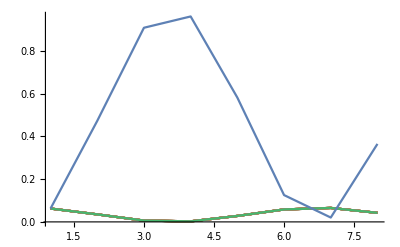

```mathematica
n=Floor[π/4 √(Dimensions[ketψ][[1]])];
Subscript[toplot, j_]:=Table[Abs[Subscript[ketψ, i][[j,1]]]^2,{i,0,2n+1}];
ListLinePlot[Table[Subscript[toplot, i],{i,1,16}],PlotRange->All]
```

#### Medir y probar resultado

```mathematica
RandomChoice[Flatten[Abs[Subscript[ketψ, n]]^2]->Table[i,{i,1,Dimensions[Subscript[ketψ, n]][[1]]}],20]
Position[data,buscar]
data[[Position[data,buscar][[1,1]]]]
```

{16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}

{{8}}

16

```mathematica
ketpy={{0.04385786+0.01718251ⅈ},{0.04385903+0.01871841ⅈ},{0.04416878+0.01788392ⅈ},{0.04078101+0.0179837ⅈ},{0.04484754+0.01727529ⅈ},{0.04376843+0.01714676ⅈ},{0.04545046+0.01778348ⅈ},{0.04430157+0.01591849ⅈ},{0.044559+0.01583714ⅈ},{0.04386416+0.01736248ⅈ},{0.04452687+0.01660607ⅈ},{0.04365657+0.01640511ⅈ},{0.04576539+0.01645807ⅈ},{0.04342327+0.01660721ⅈ},{0.04312597+0.01726914ⅈ},{-0.90667239-0.38012854ⅈ}};
```

```mathematica
Abs[ketpy†.Subscript[ketψ, 3]]
```

{{0.999875}}

```mathematica
ketpyy={{0.08201454-0.18928292I},{0.08198888-0.18932485I},{0.08211445-0.18901311I},{0.0821375-0.18961576I},{0.08192332-0.18928866I},{0.08218462-0.18917131I},{0.08232985-0.18986378I},{0.08273714-0.18906296I},{0.08199489-0.18936172I},{0.08214138-0.19012357I},{0.08185422-0.18903717I},{0.08216521-0.18920655I},{0.08151934-0.18883144I},{0.08193873-0.18950729I},{0.08146689-0.18961357I},{0.23455004-0.5533692I}};
Abs[ketpyy†.Subscript[ketψ, 7]]
```

{{0.999984}}

```mathematica
rhoy={{0.09841622+1.33803715*^-12I,0.01635126-9.72582693*^-04I,-0.00283235-1.19202572*^-03I,-0.00958269+6.59534151*^-05I,-0.00726883-1.02013469*^-03I,-0.01063294-9.23109373*^-05I,-0.00851872-1.17330835*^-03I,-0.00764291+3.99236814*^-04I,0.02722142-4.25356305*^-04I,0.00046277+1.86031802*^-03I,-0.00575172-1.11278615*^-03I,-0.00691343+8.29590129*^-05I,-0.00623901-9.47587571*^-04I,-0.00713644+2.38167243*^-06I,-0.00771419-1.45756606*^-03I,-0.00061321+1.43632685*^-04I},{0.01635126+9.72582694*^-04I,0.07084926-1.67652871*^-13I,-0.00643484+6.20851053*^-04I,0.00130985-6.25843761*^-04I,-0.00772136-6.99151083*^-04I,-0.00050034-4.93664481*^-04I,-0.00507844-2.95076765*^-04I,0.00033825+1.87237764*^-04I,0.00266962-1.12904107*^-03I,0.02424541-1.78195957*^-03I,-0.00353561+3.08210500*^-04I,0.00080991-7.74085847*^-04I,-0.00398406-6.38235875*^-04I,0.00034875-8.72422340*^-04I,-0.00202833+1.40246608*^-04I,0.00406839+9.00154072*^-04I},{-0.00283235+1.19202572*^-03I,-0.00643484-6.20851054*^-04I,0.07103304-6.21644381*^-13I,0.01617625-5.68229349*^-04I,-0.0052301+9.26914117*^-04I,-0.00448908-3.13588522*^-04I,0.00124053-1.33325071*^-03I,-0.00071037-4.44679826*^-04I,-0.00335811-1.99927002*^-06I,-0.00361046-1.74060160*^-04I,0.02299061-9.64141992*^-04I,0.00485003+3.55110988*^-04I,-0.00238627+4.46544738*^-04I,-0.00064985-3.99126633*^-04I,0.00159711-1.46122146*^-03I,0.00369313+2.32260421*^-06I},{-0.00958269-6.59534137*^-05I,0.00130985+6.25843760*^-04I,0.01617625+5.68229348*^-04I,0.05623179+4.71614745*^-14I,-0.0037189+1.03275230*^-04I,0.00248776+2.96937793*^-04I,0.0001078+2.66022907*^-04I,0.00602309-3.74760620*^-04I,-0.00380013-2.47308120*^-04I,0.00214189-1.27885704*^-04I,0.00704608-8.70384204*^-05I,0.02200357+2.45846555*^-04I,-0.00035004-1.91572045*^-04I,0.00453146+2.75676808*^-04I,0.00215719+7.73975329*^-05I,0.00820245+9.89628675*^-04I},{-0.00726883+1.02013469*^-03I,-0.00772136+6.99151083*^-04I,-0.0052301-9.26914117*^-04I,-0.0037189-1.03275230*^-04I,0.07506231-1.92634551*^-13I,0.0169543-8.34235363*^-04I,0.00325102-6.84982142*^-04I,-0.00048324+2.74485309*^-04I,-0.00386006+2.79318485*^-05I,-0.0029979+5.42111138*^-04I,-0.001867-1.75603951*^-04I,-0.00031528+1.29910482*^-04I,0.02402637-1.48570290*^-03I,0.00523069+1.07374328*^-03I,0.00146873-1.09937601*^-03I,0.00456181+4.98303903*^-06I},{-0.01063294+9.23109386*^-05I,-0.00050034+4.93664481*^-04I,-0.00448908+3.13588521*^-04I,0.00248776-2.96937794*^-04I,0.0169543+8.34235363*^-04I,0.05944317+4.93357278*^-13I,0.00069254+8.46252446*^-04I,0.0063754+3.06712568*^-05I,-0.00320442-1.98924888*^-04I,0.00232213-1.04436865*^-04I,0.00014386+5.49348433*^-04I,0.00455427-4.64241786*^-04I,0.007368-1.16211206*^-03I,0.02168913-2.16196666*^-03I,0.00285773+9.81204999*^-04I,0.00790237+5.28964470*^-04I},{-0.00851872+1.17330835*^-03I,-0.00507844+2.95076765*^-04I,0.00124053+1.33325071*^-03I,0.0001078-2.66022907*^-04I,0.00325102+6.84982141*^-04I,0.00069254-8.46252446*^-04I,0.0609781+1.23161592*^-13I,0.01740442-1.64834045*^-03I,-0.00229082+1.07645294*^-03I,-0.00033118+1.41564574*^-04I,0.00261896+1.65646374*^-04I,0.00308279-3.45612147*^-04I,0.00334591+7.01722882*^-04I,0.00363387+1.68110073*^-04I,0.02285403-2.22041623*^-03I,0.00949688+1.24344840*^-04I},{-0.00764291-3.99236812*^-04I,0.00033825-1.87237765*^-04I,-0.00071037+4.44679826*^-04I,0.00602309+3.74760619*^-04I,-0.00048324-2.74485310*^-04I,0.0063754-3.06712580*^-05I,0.01740442+1.64834045*^-03I,0.05412439-3.63965633*^-13I,-0.00068938-5.35509890*^-05I,0.00393134-3.20648342*^-04I,0.00347383+4.32349364*^-04I,0.00642426-8.34220018*^-04I,0.00313889-5.52129144*^-04I,0.00747238-2.68897690*^-04I,0.00941521+6.26411129*^-04I,0.02033132-2.03089353*^-03I},{0.02722142+4.25356306*^-04I,0.00266962+1.12904107*^-03I,-0.00335811+1.99927006*^-06I,-0.00380013+2.47308120*^-04I,-0.00386006-2.79318482*^-05I,-0.00320442+1.98924888*^-04I,-0.00229082-1.07645294*^-03I,-0.00068938+5.35509891*^-05I,0.06535957+2.32244065*^-13I,0.01309767+1.22021571*^-04I,0.00285052+1.44226622*^-04I,-0.00129075+3.01293264*^-04I,0.0011475+8.01307000*^-04I,-0.00171935+4.09767011*^-04I,0.00017413-1.12059431*^-03I,0.00444501-6.82813257*^-04I},{0.00046277-1.86031802*^-03I,0.02424541+1.78195957*^-03I,-0.00361046+1.74060159*^-04I,0.00214189+1.27885703*^-04I,-0.0029979-5.42111138*^-04I,0.00232213+1.04436864*^-04I,-0.00033118-1.41564574*^-04I,0.00393134+3.20648341*^-04I,0.01309767-1.22021572*^-04I,0.05360147+4.75339399*^-15I,0.00040211+8.37063088*^-04I,0.00495565-5.02331546*^-04I,0.00048854-7.29802340*^-05I,0.00404733+1.36634761*^-04I,0.00185158+4.43545165*^-04I,0.00770765+3.24824375*^-04I},{-0.00575172+1.11278615*^-03I,-0.00353561-3.08210501*^-04I,0.02299061+9.64141991*^-04I,0.00704608+8.70384185*^-05I,-0.001867+1.75603952*^-04I,0.00014386-5.49348433*^-04I,0.00261896-1.65646375*^-04I,0.00347383-4.32349365*^-04I,0.00285052-1.44226623*^-04I,0.00040211-8.37063089*^-04I,0.05234266-1.19600865*^-13I,0.01348421-5.71895602*^-04I,0.00324125+3.88855189*^-04I,0.00292066-7.16453998*^-04I,0.00600376+1.51368263*^-04I,0.00659833-2.05950587*^-04I},{-0.00691343-8.29590106*^-05I,0.00080991+7.74085847*^-04I,0.00485003-3.55110989*^-04I,0.02200357-2.45846557*^-04I,-0.00031528-1.29910482*^-04I,0.00455427+4.64241785*^-04I,0.00308279+3.45612146*^-04I,0.00642426+8.34220016*^-04I,-0.00129075-3.01293264*^-04I,0.00495565+5.02331545*^-04I,0.01348421+5.71895601*^-04I,0.0470757-5.84909496*^-13I,0.00265022-1.63801616*^-04I,0.00784468+7.12046346*^-05I,0.0049778+6.34677486*^-04I,0.01037179+1.47232505*^-03I},{-0.00623901+9.47587572*^-04I,-0.00398406+6.38235876*^-04I,-0.00238627-4.46544739*^-04I,-0.00035004+1.91572045*^-04I,0.02402637+1.48570289*^-03I,0.007368+1.16211206*^-03I,0.00334591-7.01722883*^-04I,0.00313889+5.52129143*^-04I,0.0011475-8.01307001*^-04I,0.00048854+7.29802332*^-05I,0.00324125-3.88855190*^-04I,0.00265022+1.63801616*^-04I,0.0563778-6.85634182*^-13I,0.01381629-4.45971311*^-04I,0.00659943-4.73889785*^-04I,0.00706574-3.07325733*^-04I},{-0.00713644-2.38167130*^-06I,0.00034875+8.72422339*^-04I,-0.00064985+3.99126632*^-04I,0.00453146-2.75676809*^-04I,0.00523069-1.07374328*^-03I,0.02168913+2.16196666*^-03I,0.00363387-1.68110073*^-04I,0.00747238+2.68897689*^-04I,-0.00171935-4.09767011*^-04I,0.00404733-1.36634762*^-04I,0.00292066+7.16453997*^-04I,0.00784468-7.12046353*^-05I,0.01381629+4.45971310*^-04I,0.04998881-2.18263115*^-13I,0.00566181+7.72324134*^-04I,0.0115641+5.79622998*^-04I},{-0.00771419+1.45756606*^-03I,-0.00202833-1.40246608*^-04I,0.00159711+1.46122146*^-03I,0.00215719-7.73975331*^-05I,0.00146873+1.09937601*^-03I,0.00285773-9.81204999*^-04I,0.02285403+2.22041623*^-03I,0.00941521-6.26411130*^-04I,0.00017413+1.12059431*^-03I,0.00185158-4.43545166*^-04I,0.00600376-1.51368263*^-04I,0.0049778-6.34677486*^-04I,0.00659943+4.73889784*^-04I,0.00566181-7.72324135*^-04I,0.05588314+6.99844389*^-14I,0.01592677+6.10949686*^-04I},{-0.00061321-1.43632684*^-04I,0.00406839-9.00154073*^-04I,0.00369313-2.32260514*^-06I,0.00820245-9.89628676*^-04I,0.00456181-4.98303974*^-06I,0.00790237-5.28964471*^-04I,0.00949688-1.24344841*^-04I,0.02033132+2.03089353*^-03I,0.00444501+6.82813256*^-04I,0.00770765-3.24824377*^-04I,0.00659833+2.05950585*^-04I,0.01037179-1.47232505*^-03I,0.00706574+3.07325732*^-04I,0.0115641-5.79622999*^-04I,0.01592677-6.10949687*^-04I,0.07323257+6.45570169*^-13I}};
```

```mathematica
√Abs[ketpy†.rhoy.ketpy]
```

{{0.250818}}

```mathematica
rhopy1={{0.04875766+5.52244239*^-12I,0.01756872-2.27082486*^-03I,0.0125092-1.10087901*^-03I,0.0051625+4.58954419*^-05I,0.01210125-3.03984413*^-04I,0.00350501-1.53256563*^-04I,0.00374522-4.65218344*^-04I,0.00393789+1.44199387*^-03I,0.02567023-8.70017624*^-04I,0.00925742+6.05007512*^-04I,0.00756184-1.11742990*^-03I,0.00432005+1.14016291*^-03I,0.00968133+3.89116188*^-04I,0.00454383+5.35107033*^-04I,0.004893-2.42924901*^-03I,0.02224585+8.19433883*^-04I},{0.01756872+2.27082486*^-03I,0.05192874-4.86846152*^-13I,0.00857355+2.28128137*^-03I,0.01825149-1.85921982*^-03I,0.00758579+5.28776168*^-04I,0.01857531+5.37078021*^-04I,0.00865466+2.33603375*^-03I,0.01755724-4.13562842*^-05I,0.01281777+9.28826756*^-04I,0.03489145-1.91793613*^-03I,0.00970158+1.44071327*^-03I,0.01684523+3.95733542*^-04I,0.01052514-2.16702754*^-03I,0.01807775+5.71659814*^-04I,0.01329057+7.42314563*^-05I,0.03935789+3.99353414*^-03I},{0.0125092+1.10087901*^-03I,0.00857355-2.28128137*^-03I,0.04571251-1.07854295*^-12I,0.02233878-4.11499526*^-03I,0.00626565+8.27935195*^-04I,0.00752051-1.61417912*^-03I,0.01726265-1.11354333*^-03I,0.01509223-3.03216674*^-03I,0.01046694+8.44389199*^-04I,0.00926819-3.70582142*^-04I,0.02930984-1.85939056*^-03I,0.01662287-2.10451846*^-03I,0.01036239+1.84694973*^-03I,0.01432064-1.76466755*^-03I,0.01706602-2.01034505*^-03I,0.03506659+5.66540243*^-04I},{0.0051625-4.58954397*^-05I,0.01825149+1.85921981*^-03I,0.02233878+4.11499526*^-03I,0.05503895-4.02564603*^-12I,0.00873533+1.71569759*^-03I,0.01845591+2.43067309*^-03I,0.01680518+3.41702148*^-03I,0.02793408+8.90437752*^-04I,0.00965093-5.20648302*^-04I,0.01949968+4.35131068*^-03I,0.02072061+4.48809957*^-03I,0.04145084+7.08304990*^-04I,0.01497511+1.89076196*^-04I,0.02545889+3.79931924*^-03I,0.02097959+1.68044418*^-03I,0.05008298+6.28408946*^-03I},{0.01210125+3.03984417*^-04I,0.00758579-5.28776172*^-04I,0.00626565-8.27935196*^-04I,0.00873533-1.71569759*^-03I,0.04697299+1.43636194*^-13I,0.02252868-1.87112433*^-03I,0.01824286-6.22869725*^-04I,0.01549666-1.69210293*^-05I,0.0150135+1.76909682*^-03I,0.01150225+1.11965531*^-03I,0.01057045+1.39497764*^-03I,0.01367568-2.78050790*^-04I,0.02954044+3.01880466*^-04I,0.01795077+5.82457421*^-04I,0.01765027-4.71951948*^-04I,0.03558254+5.62423664*^-04I},{0.00350501+1.53256571*^-04I,0.01857531-5.37078021*^-04I,0.00752051+1.61417912*^-03I,0.01845591-2.43067310*^-03I,0.02252868+1.87112433*^-03I,0.05566352+7.67502441*^-13I,0.0171915+2.08959216*^-03I,0.02825863-1.10726914*^-03I,0.01200764+1.43329138*^-03I,0.02326337+1.96587159*^-03I,0.0149233+3.34768754*^-03I,0.02363195+1.28315388*^-04I,0.02304718+1.05873894*^-03I,0.04162284-2.90145840*^-03I,0.02251847+2.72822977*^-03I,0.05103494+2.23700379*^-03I},{0.00374522+4.65218348*^-04I,0.00865466-2.33603374*^-03I,0.01726265+1.11354333*^-03I,0.01680518-3.41702148*^-03I,0.01824286+6.22869725*^-04I,0.0171915-2.08959216*^-03I,0.0485806+5.02975398*^-13I,0.031383-4.59752839*^-03I,0.01104934+2.47908399*^-03I,0.01491839-6.57035143*^-04I,0.02102033+1.91573504*^-03I,0.02133387-1.38530358*^-03I,0.01927545+2.65851989*^-03I,0.02292614-2.32446787*^-04I,0.036113-1.76508463*^-03I,0.04931661-2.00948176*^-03I},{0.00393789-1.44199387*^-03I,0.01755724+4.13562855*^-05I,0.01509223+3.03216674*^-03I,0.02793408-8.90437756*^-04I,0.01549666+1.69210285*^-05I,0.02825863+1.10726914*^-03I,0.031383+4.59752839*^-03I,0.06783093+9.57930453*^-13I,0.01494341-3.98112402*^-04I,0.0248621+2.37045211*^-03I,0.02273223+3.88327911*^-03I,0.03276814+1.81004057*^-04I,0.02317043+5.03867546*^-04I,0.03448261+1.38380113*^-03I,0.0332804+3.44822935*^-03I,0.07997706-3.32251334*^-03I},{0.02567023+8.70017633*^-04I,0.01281777-9.28826765*^-04I,0.01046694-8.44389198*^-04I,0.00965093+5.20648295*^-04I,0.0150135-1.76909681*^-03I,0.01200764-1.43329138*^-03I,0.01104934-2.47908398*^-03I,0.01494341+3.98112409*^-04I,0.04909442+3.74770515*^-12I,0.023698-2.14978383*^-03I,0.02216418+8.73512402*^-05I,0.01644759-1.65047997*^-04I,0.02270252+1.15172518*^-03I,0.01727966-1.58731965*^-05I,0.01861698-1.51001439*^-03I,0.03888888-2.40594787*^-03I},{0.00925742-6.05007507*^-04I,0.03489145+1.91793612*^-03I,0.00926819+3.70582140*^-04I,0.01949968-4.35131068*^-03I,0.01150225-1.11965531*^-03I,0.02326337-1.96587159*^-03I,0.01491839+6.57035142*^-04I,0.0248621-2.37045211*^-03I,0.023698+2.14978383*^-03I,0.05815722+2.90086959*^-13I,0.01893505+2.21671363*^-03I,0.02696213-2.04895811*^-03I,0.02117996+3.07479087*^-04I,0.02941994-4.39368380*^-04I,0.02364684+1.56752464*^-03I,0.05333793-1.56422670*^-04I},{0.00756184+1.11742991*^-03I,0.00970158-1.44071329*^-03I,0.02930984+1.85939056*^-03I,0.02072061-4.48809958*^-03I,0.01057045-1.39497763*^-03I,0.0149233-3.34768753*^-03I,0.02102033-1.91573504*^-03I,0.02273223-3.88327911*^-03I,0.02216418-8.73512337*^-05I,0.01893505-2.21671363*^-03I,0.05056593+2.60759723*^-12I,0.02913865-4.34116482*^-03I,0.02119535+6.22900078*^-04I,0.02398491-3.20089186*^-03I,0.02859683-1.11812895*^-03I,0.04921872-1.25371866*^-03I},{0.00432005-1.14016289*^-03I,0.01684523-3.95733552*^-04I,0.01662287+2.10451845*^-03I,0.04145084-7.08305003*^-04I,0.01367568+2.78050813*^-04I,0.02363195-1.28315396*^-04I,0.02133387+1.38530357*^-03I,0.03276814-1.81004066*^-04I,0.01644759+1.65047994*^-04I,0.02696213+2.04895810*^-03I,0.02913865+4.34116481*^-03I,0.06340171-8.61948880*^-12I,0.02356355+1.96939263*^-03I,0.03400011+1.20650382*^-03I,0.03031759+2.22102272*^-03I,0.06409574+3.79724720*^-03I},{0.00968133-3.89116191*^-04I,0.01052514+2.16702755*^-03I,0.01036239-1.84694974*^-03I,0.01497511-1.89076178*^-04I,0.02954044-3.01880472*^-04I,0.02304718-1.05873894*^-03I,0.01927545-2.65851990*^-03I,0.02317043-5.03867551*^-04I,0.02270252-1.15172519*^-03I,0.02117996-3.07479088*^-04I,0.02119535-6.22900081*^-04I,0.02356355-1.96939265*^-03I,0.05471996-6.33066339*^-12I,0.03201926-3.16644583*^-03I,0.02862253-1.83856388*^-04I,0.04924898-1.00393545*^-03I},{0.00454383-5.35107026*^-04I,0.01807775-5.71659815*^-04I,0.01432064+1.76466756*^-03I,0.02545889-3.79931924*^-03I,0.01795077-5.82457423*^-04I,0.04162284+2.90145839*^-03I,0.02292614+2.32446785*^-04I,0.03448261-1.38380114*^-03I,0.01727966+1.58731947*^-05I,0.02941994+4.39368379*^-04I,0.02398491+3.20089186*^-03I,0.03400011-1.20650383*^-03I,0.03201926+3.16644582*^-03I,0.06857713-3.11120315*^-12I,0.03228525+1.91873985*^-03I,0.06660358+1.67195213*^-03I},{0.004893+2.42924901*^-03I,0.01329057-7.42314411*^-05I,0.01706602+2.01034505*^-03I,0.02097959-1.68044417*^-03I,0.01765027+4.71951943*^-04I,0.02251847-2.72822977*^-03I,0.036113+1.76508463*^-03I,0.0332804-3.44822935*^-03I,0.01861698+1.51001439*^-03I,0.02364684-1.56752465*^-03I,0.02859683+1.11812895*^-03I,0.03031759-2.22102274*^-03I,0.02862253+1.83856379*^-04I,0.03228525-1.91873985*^-03I,0.06153266-5.17653768*^-12I,0.06663966-2.49793976*^-03I},{0.02224585-8.19433926*^-04I,0.03935789-3.99353413*^-03I,0.03506659-5.66540230*^-04I,0.05008298-6.28408945*^-03I,0.03558254-5.62423676*^-04I,0.05103494-2.23700377*^-03I,0.04931661+2.00948178*^-03I,0.07997706+3.32251336*^-03I,0.03888888+2.40594788*^-03I,0.05333793+1.56422684*^-04I,0.04921872+1.25371868*^-03I,0.06409574-3.79724720*^-03I,0.04924898+1.00393546*^-03I,0.06660358-1.67195212*^-03I,0.06663966+2.49793977*^-03I,0.17346507+1.42890168*^-11I}};
```

```mathematica
√Abs[Subscript[ketψ, 1]†.rhopy1.Subscript[ketψ, 1]]
```

{{0.666611}}